# Mathematical calculations for the Double Pendulum Simulation

Here I will discuss how the analytical system works.

Let’s start by considering an example system:
We define the angle θ and the angle ϕ respect to the vertical, as shown in the figure below.
Each rod as a length of  and mass .

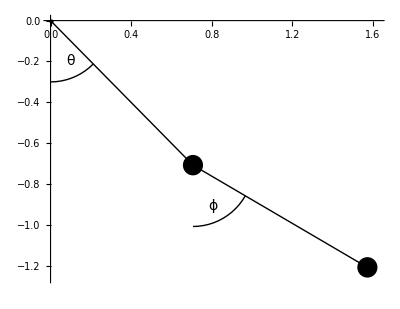

```mathematica
(*Example*)
a=π/4; 
b=π/3; 

x1=Sin[a];
y1=-Cos[a];
x2=x1+ Sin[b];
y2=y1- Cos[b];

Graphics[{Thick,Line[{{0,0},{x1,y1}}],Line[{{x1,y1},{x2,y2}}],Disk[{x1,y1},0.05],Disk[{x2,y2},0.05],Black,Point[{0,0}],
Circle[{0,0},0.3,{3/2π,3/2π+a}],Circle[{x1,y1},0.3,{3/2π,3/2π+b}],
Text[Style["θ",14],{0.1,-0.2}],Text[Style["ϕ",14],{x1+0.1,y1-0.2}]
},PlotRange->{{0, 2}, {0,- 2}},Axes->True,AxesOrigin->{0,0}]
```

So we have the generalized  coordinates , which  uniquely  describe  the  two  points   .
For simplicity and to reduce computations we will set  and .

From  and  we  can  calculate  the  kinetic  energy :

```mathematica
T [θ_,ϕ_,θ_',ϕ_']:= 1/2(2 θ'^2 + ϕ'^2+ 2Cos[θ-ϕ]θ'ϕ')
```

And the potential energy:

```mathematica
V[θ_, ϕ_]:= g(2Cos[θ]+Cos[ϕ])
```

So we can get the Lagrangian:

```mathematica
L[θ_,ϕ_,θ_',ϕ_']:= T[θ,ϕ,θ',ϕ'] - V[θ,ϕ]
Collect[FullSimplify[L [θ,ϕ, θ',ϕ']], {θ',ϕ', g}]
```

g (-2 Cos[θ]-Cos[ϕ])+(θ')^2+Cos[θ-ϕ] θ' ϕ'+(ϕ')^2/2

By calculating the partial derivatives of the Lagrangian  respect to  and  we get the associated moments  and .

```mathematica
M={Coefficient[D[L[θ,ϕ,θ',ϕ'] ,θ'], {θ', ϕ'}],Coefficient[D[L[θ,ϕ,θ',ϕ'], ϕ'], {θ', ϕ'}]};
MatrixForm[M]
```

(2 | Cos[θ-ϕ]
Cos[θ-ϕ] | 1)

We now have that .
We can invert  the matrix to find  and  respect to   and .

```mathematica
Inv = Inverse[M];
MatrixForm[Inv]
```

(-1/(-2+Cos[θ-ϕ]^2) | Cos[θ-ϕ]/(-2+Cos[θ-ϕ]^2)
Cos[θ-ϕ]/(-2+Cos[θ-ϕ]^2) | -2/(-2+Cos[θ-ϕ]^2))

We can calculate the Jacobian of the system:

```mathematica
J [θ_,ϕ_,θ_',ϕ_', Pθ_,Pϕ_ ]:= Pθ θ' + Pϕ ϕ' - L[θ,ϕ,θ',ϕ']
FullSimplify[J[θ,ϕ,θ',ϕ', Pθ,Pϕ]]
```

g (2 Cos[θ]+Cos[ϕ])-(θ')^2+Pϕ ϕ'-(ϕ')^2/2+θ' (Pθ-Cos[θ-ϕ] ϕ')

By substituting  and  in the Jacobian we get the Hamiltonian of the system.

```mathematica
H [θ_,ϕ_, Pθ_,Pϕ_]:={Pθ θ' + Pϕ ϕ' - L[θ,ϕ,θ',ϕ']}/. {θ' -> Inv[[1,1]]Pθ +Inv[[1,2]]Pϕ  , ϕ' ->  Inv[[2,1]]Pθ +Inv[[2,2]]Pϕ  }
Collect[FullSimplify[H [θ,ϕ, Pθ,Pϕ]], {Pθ, Pϕ, g}]
```

{-Pθ^2/(-3+Cos[2 (θ-ϕ)])-(2 Pϕ^2)/(-3+Cos[2 (θ-ϕ)])+(2 Pθ Pϕ Cos[θ-ϕ])/(-3+Cos[2 (θ-ϕ)])+g (2 Cos[θ]+Cos[ϕ])}

From the Hamiltonian we can simply get the 4 equation of motion by calculating the partial derivatives of the Hamiltonian:

```mathematica
Collect[FullSimplify[-D[H[θ,ϕ, Pθ,Pϕ], Pθ]], {Pθ, Pϕ, g}]
Collect[FullSimplify[-D[H[θ,ϕ, Pθ,Pϕ], Pϕ]], {Pθ, Pϕ, g}]
Collect[FullSimplify[D[H[θ,ϕ, Pθ,Pϕ], θ]], {Pθ, Pϕ, g}]
Collect[FullSimplify[D[H[θ,ϕ, Pθ,Pϕ], ϕ]], {Pθ, Pϕ,g}]
```

{Pθ/(-2+Cos[θ-ϕ]^2)-(Pϕ Cos[θ-ϕ])/(-2+Cos[θ-ϕ]^2)}

{(2 Pϕ)/(-2+Cos[θ-ϕ]^2)-(Pθ Cos[θ-ϕ])/(-2+Cos[θ-ϕ]^2)}

{-(g (-3+Cos[2 (θ-ϕ)])^2 Sin[θ])/(2 (-2+Cos[θ-ϕ]^2)^2)-(Pθ^2 Cos[θ-ϕ] Sin[θ-ϕ])/((-2+Cos[θ-ϕ]^2)^2)-(2 Pϕ^2 Cos[θ-ϕ] Sin[θ-ϕ])/((-2+Cos[θ-ϕ]^2)^2)+(Pθ Pϕ (5+Cos[2 (θ-ϕ)]) Sin[θ-ϕ])/(2 (-2+Cos[θ-ϕ]^2)^2)}

{-(2 Pθ Pϕ (5+Cos[2 (θ-ϕ)]) Sin[θ-ϕ])/(-3+Cos[2 (θ-ϕ)])^2+(2 Pθ^2 Sin[2 (θ-ϕ)])/(-3+Cos[2 (θ-ϕ)])^2+(4 Pϕ^2 Sin[2 (θ-ϕ)])/(-3+Cos[2 (θ-ϕ)])^2-g Sin[ϕ]}

So those are our equations to calculate the movements of the pendulums. We can actually write them a bit better by defining:








In this way we have the four equations:





These equations are ready to be put in our system integrator.